```mathematica
ClearAll["Global`*"]
```

# Preheating scenario

```mathematica
(* adimensional time *)
zIn=2/3;          
zMax=25;         

(* q parameter: Broad resonance *)
q=10^4;
Print["\n coupling value g = ",g = Sqrt[(q*4*(6*10^-6)^2)/2.32^2]]
```

coupling value g = 0.000517241

## Solving Background dynamic

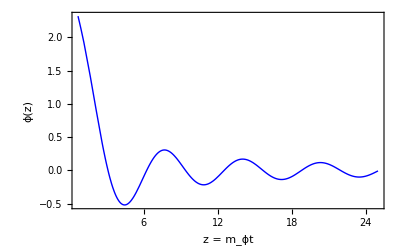

```mathematica
(* Hubble factor: matter era *)
H[z_]:=2/(3z);

(* Solution Inflaton *) 
eqϕ=ϕ''[z]+3*H[z]*ϕ'[z]+ϕ[z]==0;
ϕIn=2.32;                         (* in units of reduced Planck mass *)
dϕIn=-0.78;                    (* in units of reduced Planck mass *)
bcϕ={ϕ[zIn]==ϕIn,ϕ'[zIn]==dϕIn};
solϕ=DSolveValue[{eqϕ,bcϕ},ϕ,z]//FullSimplify;

(* Plots *)
ϕplot =Plot[solϕ[z],{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z = m_ϕt","Times"]}],15,"Times"],Style[Row[{Style["ϕ(z)","Times"]}],15,"Times"]},PlotStyle->{Blue,Thick}]
```

```mathematica
(* Period *)
FunctionPeriod[solϕ[z]*z,z]
```

2 π

## Fit

{a→2.37322,b→1.52762}

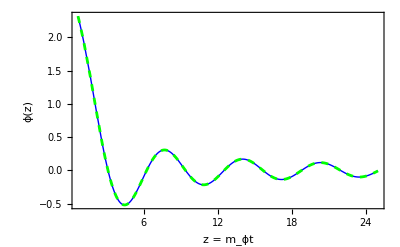

```mathematica
solϕnumerical=NDSolveValue[{eqϕ,bcϕ},ϕ,{z,zIn,zMax}];
dataInflaton=Table[{zVal,solϕnumerical[zVal]},{zVal,zIn,zMax,0.1}];

fitParams=FindFit[dataInflaton,(a/z)*Cos[z-b],{a,b},z]

fitplot = Plot[(a/z)*Cos[z-b]/.fitParams,{z,zIn,zMax},PlotStyle->{Dashed,Green},PlotRange->All];
Show[{ϕplot,fitplot}]
```

## Resonance parameter

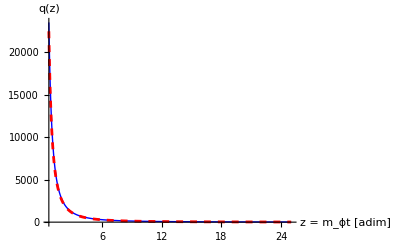

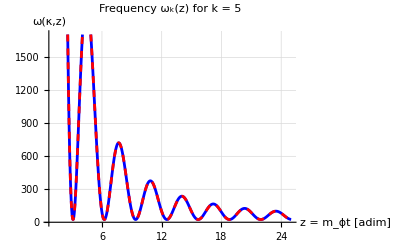

```mathematica
(* q effective in expanding universe *)
qeff[z_]:=q*((a/(z+b))/ϕIn)^2 /. fitParams;

bpar = b/.fitParams[[2]];
(* Plot q effective *)
qPlot = Plot[{qeff[z-bpar],q*(z^-2)},{z,zIn,zMax},PlotRange->All,AxesLabel->{"z = m_ϕt [adim]","q(z)"},PlotStyle->{{Thick,Blue},{Dashed,Red}}]

Apar[z_,k_]:=k^2 + 2qeff[z];
ωMathieu[z_,k_]:=Apar[z,k]+ 2qeff[z]Cos[2z];

ω2[z_,k_]:=k^2+4*q*(solϕ[z]/ϕIn)^2;

(* Plot equivalence *)
ωPlot1 = Plot[ωMathieu[z-bpar,5],{z,zIn,zMax},PlotStyle->{Dashed,Red}];
ω2Plot = Plot[ω2[z,5],{z,zIn,zMax},PlotStyle->{Blue},AxesLabel->{"z = m_ϕt [adim]","ω(κ,z)"},PlotLabel->Style[StringForm["Frequency ω_k(z) for k = ``",5]],PlotStyle->{Blue,Thick},GridLines->Automatic];
Show[{ω2Plot,ωPlot1}]
```

## Stability / Instability chart and Time evolution

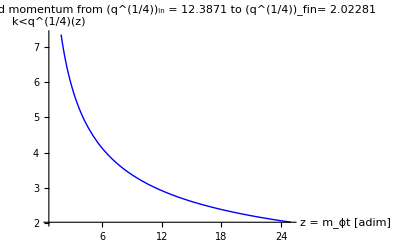

```mathematica
Plot[qeff[z-bpar]^(1/4),{z,zIn,zMax},AxesLabel->{"z = m_ϕt [adim]","k<q^(1/4)(z)"},PlotLabel->Style[StringForm["Excited momentum from (q^(1/4))_in = `` to (q^(1/4))_fin= ``",qeff[zIn-bpar]^(1/4),qeff[zMax-bpar]^(1/4)]],PlotStyle->{Thick,Blue}]
```

## Daughter dynamic

```mathematica
(* Solution Spectator *) 
eqχ=χ''[z]+ω2[z,k]*χ[z]==0;
bcχ={χ[zIn]==1/(√(2Sqrt[ω2[zIn,k]])),χ'[zIn]==-I √(Sqrt[ω2[zIn,k]]/2)};
solχ=ParametricNDSolveValue[{eqχ,bcχ[[1]],bcχ[[2]]},χ,{z,zIn,zMax},{k},MaxSteps->Infinity,Method->"StiffnessSwitching"];
χsol[k_,z_]:=solχ[k][z];

(* Number density spectator *)
numberχ[k_,z_] := Module[{χsolK},
χsolK = solχ[k];
Abs[χsolK'[z]]^2/(2*Sqrt[ω2[z,k]])+Sqrt[ω2[z,k]]/2 Abs[χsolK[z]]^2-1/2
];
```

## Plots

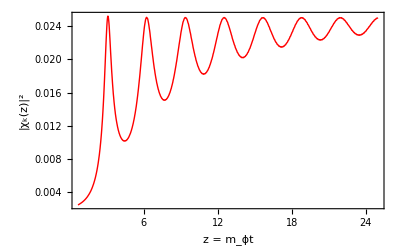

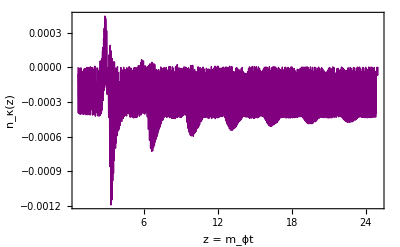

```mathematica
plotχ2 =Plot[Abs[χsol[20,z]]^2,{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z = m_ϕt","Times"]}],15,"Times"],Style[Row[{Style["|χ_k(z)|^2","Times"]}],15,"Times"]},PlotStyle->{Red,Thick}]
plotnχ2 =Plot[numberχ[20,z],{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z = m_ϕt","Times"]}],15,"Times"],Style[Row[{Style["n_κ(z)","Times"]}],15,"Times"]},PlotStyle->{Purple,Thick}]
```

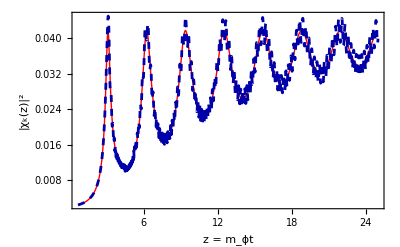

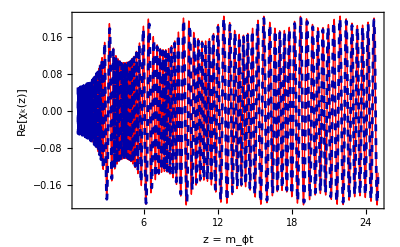

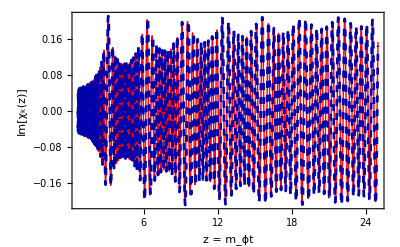

```mathematica
(* κ>12 Equivalent to vacuum evolution *)

(*fase del vuoto dinamico θ'[z]*)
eqθ=θ'[z]==Sqrt[ω2[z,k]];
bcθ=θ[zIn]==0;
solθ=ParametricNDSolveValue[{eqθ,bcθ},θ,{z,zIn,zMax},{k},MaxSteps->Infinity,Method->"StiffnessSwitching"];
θsol[k_,z_]:=solθ[k][z];

(*Vacuum mode function*)
χvac[k_,z_]:=Exp[-I*θsol[k,z]]/Sqrt[2*Sqrt[ω2[z,k]]];

plotdiffχvacuum =Plot[{Abs[χvac[12,z]]^2,Abs[χsol[12,z]]^2},{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z = m_ϕt","Times"]}],15,"Times"],Style[Row[{Style["|χ_k(z)|^2","Times"]}],15,"Times"]},PlotStyle->{{Red,Thick},{Dashed,Darker[Blue]}}]

plotReχvacuum =Plot[{Re[χvac[12,z]],Re[χsol[12,z]]},{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z = m_ϕt","Times"]}],15,"Times"],Style[Row[{Style["Re[χ_k(z)]","Times"]}],15,"Times"]},PlotStyle->{{Red,Thick},{Dashed,Darker[Blue]}}]

plotImχvacuum =Plot[{Im[χvac[12,z]],Im[χsol[12,z]]},{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z = m_ϕt","Times"]}],15,"Times"],Style[Row[{Style["Im[χ_k(z)]","Times"]}],15,"Times"]},PlotStyle->{{Red,Thick},{Dashed,Darker[Blue]}}]
```

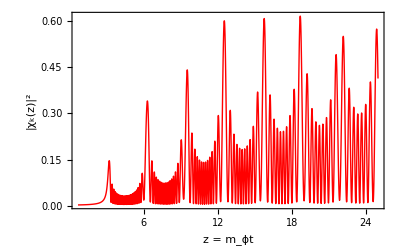

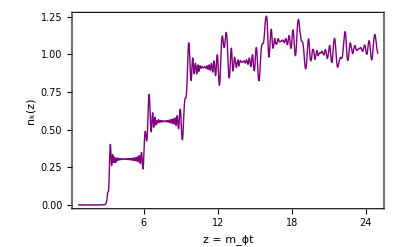

```mathematica
plotχ5 = Plot[Abs[χsol[5,z]]^2,{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z = m_ϕt","Times"]}],15,"Times"],Style[Row[{Style["|χ_k(z)|^2","Times"]}],15,"Times"]},PlotStyle->{Red,Thick}]
plotnχ5 =Plot[numberχ[5,z],{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z = m_ϕt","Times"]}],15,"Times"],Style[Row[{Style["n_k(z)","Times"]}],15,"Times"]},PlotStyle->{Purple,Thick}]
```

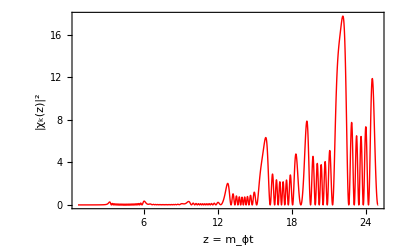

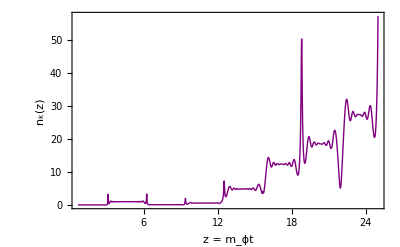

```mathematica
plotχ05 = Plot[Abs[χsol[0.5,z]]^2,{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z = m_ϕt","Times"]}],15,"Times"],Style[Row[{Style["|χ_k(z)|^2","Times"]}],15,"Times"]},PlotStyle->{Red,Thick}]
plotnχ05 = Plot[numberχ[0.5,z],{z,zIn,zMax},PlotRange->All,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["z = m_ϕt","Times"]}],15,"Times"],Style[Row[{Style["n_k(z)","Times"]}],15,"Times"]},PlotStyle->{Purple,Thick}]
```

## Power spectrum of the Daughter field

```mathematica
nχSpectrum[kList_List,z_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,numberχ[k,z]},{k,kList}],Row[{"Computation nχ for k = ",currentK}]]
];
```

```mathematica
kValsχ=Range[0.01,10,0.1];

z1 = 7;
z2 = 15;

spectrumnχ1 = nχSpectrum[kValsχ,z1];
spectrumnχ2 = nχSpectrum[kValsχ,z2];
spectrumnχ3 = nχSpectrum[kValsχ,zMax];
```

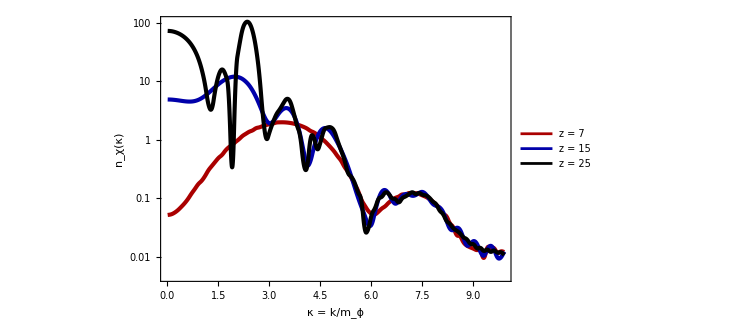

```mathematica
plotSpectranχ=ListLogPlot[{spectrumnχ1,spectrumnχ2,spectrumnχ3},Joined->True,InterpolationOrder->2,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{Style["κ = k/m_ϕ","Times"]}],15,"Times"],Style[Row[{Style["n_χ(κ)","Times"]}],15,"Times"]},PlotStyle->{{Thickness[0.0055],Darker[Red]},{Thickness[0.0055],Darker[Blue]},{Thickness[0.0055],Darker[Black]}   },PlotLegends->Placed[LineLegend[{Row[{"z = ",z1}],Row[{"z = ",z2}],Row[{"z = ",zMax}]},LegendFunction->"Frame"],{0.8,0.65}],ImageSize->540]
```

```mathematica
(* Campo fisico *)
PSχphy[k_,z_]:=  k^3/(2 π^2)(Abs[χsol[k,z]]^2  - 1/(2Sqrt[ω2[z,k]]) );
χphySpectrum[kList_List,z_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,PSχphy[k,z]},{k,kList}],Row[{"Computation χ for k = ",currentK}]]
];

PSχ[k_,z_]:=k^3/(2 π^2)  Abs[χsol[k,z]]^2 ;
χSpectrum[kList_List,z_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,PSχ[k,z]},{k,kList}],Row[{"Computation χ for k = ",currentK}]]
];
```

```mathematica
(* Log plot is not well-suited for modes with zero value 
spectrumχ1 = χSpectrum[kValsχ,z1];
spectrumχ1new = χphySpectrum[kValsχ,z1];

spectrumχ2 = χSpectrum[kValsχ,z2];
spectrumχ2new = χphySpectrum[kValsχ,z2];

spectrumχ3 = χSpectrum[kValsχ,zMax];
spectrumχ3new= χphySpectrum[kValsχ,zMax];

plotSpectrumnχ1=ListLogPlot[{spectrumχ1,spectrumχ1new},Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"κ = k/m_ϕ [adim]","χ_z(κ)"},PlotStyle->{{Thickness[0.005],Darker[Red]},{Thickness[0.005],Darker[Blue]}},GridLines->Automatic,PlotLabel->Style[StringForm["Daughter Field Power spectrum χ_z(k) at z = ``",11]]]

plotSpectrumnχ2=ListLogPlot[{spectrumχ2,spectrumχ2new},Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"κ = k/m_ϕ [adim]","χ_z(κ)"},PlotStyle->{{Thickness[0.005],Darker[Red]},{Thickness[0.005],Darker[Blue]}},GridLines->Automatic,PlotLabel->Style[StringForm["Daughter Field Power spectrum χ_z(k) at z = ``",15]]]

plotSpectrumnχ3=ListLogPlot[{spectrumχ3,spectrumχ3new},Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"κ = k/m_ϕ [adim]","χ_z(κ)"},PlotStyle->{{Thickness[0.005],Darker[Red]},{Thickness[0.005],Darker[Blue]}},GridLines->Automatic,PlotLabel->Style[StringForm["Daughter Field Power spectrum χ_z(k) at z = ``",zMax]]]
*)
```

# GW

## Compute the un-equal time Power spectrum of GWs

```mathematica
kMinGrid=0.01;
kMaxGrid=2*q^(1/4);
dk=0.1;

(* Griglia *)
nzpoints=500; 
dz=(zMax-zIn)/nzpoints;
zVals=Range[zIn,zMax,dz];

χphys[k_,z_]:=χsol[k,z]-χvac[k,z];
gridData=Flatten[Table[Table[{{kV,zV},χphys[kV,zV]},{zV,zVals}],{kV,kMinGrid,kMaxGrid,dk}],1];
χgrid=Interpolation[gridData,InterpolationOrder->3];
```

```mathematica
(* Funzioni *)
qVec[k_,p_,x_]:=Sqrt[k^2+p^2-2*k*p*x];

kCutoff = Round[qeff[zIn-bpar]^(1/4)]+1; (* < kMaxGrid *)
selectχgrid[k_,z_]:=If[k<=kMinGrid||k>=kCutoff,0.0,χgrid[k,z]];

AbsIAdimSquared[xq0_?NumericQ,xq_?NumericQ,xp_?NumericQ,x_?NumericQ]:=Block[{xqp,chiValsP,chiValsQp,productField,fourierPhase,dotProduct},
xqp=qVec[xq,xp,x];

(*If[xp>=kCutoff||xqp>=kCutoff,Return[0.0]];*)
If[xp<=kMinGrid||xp>=kCutoff||xqp<=kMinGrid||xqp>=kCutoff,Return[0]];

Quiet[
chiValsP=Map[selectχgrid[xp,#]&,zVals];
chiValsQp=Map[selectχgrid[xqp,#]&,zVals];
];

productField=chiValsP*chiValsQp;
fourierPhase=Exp[I*xq0*zVals];

dotProduct=fourierPhase.productField*dz;

Abs[dotProduct]^2
];

PΠAdim[xq0_?NumericQ,xq_?NumericQ,xpSteps_Integer:50,xSteps_Integer:20]:=Block[{xpMax,dxp,dx,xpGrid,xGrid,sumVal},
xpMax=kCutoff;
dxp=(xpMax-0.1)/xpSteps;
dx=2.0/xSteps;

xpGrid=Range[0.1,xpMax,dxp];
xGrid=Range[-1.0,1.0,dx];

Quiet[
sumVal=ParallelSum[xp^6(1-x^2)^2  AbsIAdimSquared[xq0,xq,xp,x],{xp,xpGrid},{x,xGrid}];
];

1/(4 π^2) sumVal*dxp*dx
];

PΠtoPlot[xq0_?NumericQ,xq_?NumericQ]:=xq^3 PΠAdim[xq0,xq];

Δhadim[xq0_?NumericQ,xq_?NumericQ]:=Block[{pAdimVal},
pAdimVal=PΠAdim[xq0,xq];
2/π^2 xq^3/((xq0^2 - xq^2)^2)pAdimVal
];
```

```mathematica
(* GW off-shell *)
xqPoints=Range[0.1,25,0.1];

Pq03q=Table[{xqVal,PΠtoPlot[3*xqVal,xqVal]},{xqVal,xqPoints}];
Pq05q=Table[{xqVal,PΠtoPlot[5*xqVal,xqVal]},{xqVal,xqPoints}];
Pq010q=Table[{xqVal,PΠtoPlot[10*xqVal,xqVal]},{xqVal,xqPoints}];
Pq015q=Table[{xqVal,PΠtoPlot[15*xqVal,xqVal]},{xqVal,xqPoints}];
onshellSource = Table[{xqVal,PΠtoPlot[xqVal,xqVal]},{xqVal,xqPoints}];
```

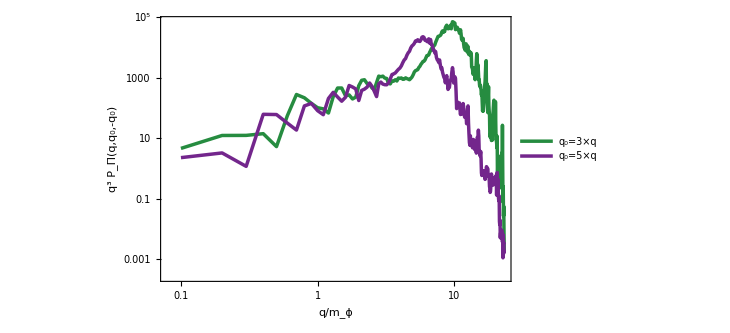

```mathematica
plotGWoffshellPreheating = ListLogLogPlot[{Pq03q,Pq05q},Joined->True,InterpolationOrder->3,Frame->True,AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[DisplayForm[FormBox[RowBox[{"q","/",Subscript["m","ϕ"]}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SuperscriptBox["q","3"],SubscriptBox["P","Π"],"(","q",",",Subscript["q","0"],",",Subscript["-q","0"],")"}],TraditionalForm]],FontSize->13]},PlotStyle->{{RGBColor[0.15,0.55,0.25],AbsoluteThickness[2.5]},{RGBColor[0.45,0.15,0.55],AbsoluteThickness[2.5]}},
PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","3×q"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","5×q"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","10×q"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","15×q"}],TraditionalForm]],FontSize->13]},LegendFunction->"Frame"],{0.6,0.25}],ImageSize->540]//Quiet
```

```mathematica
(* for z = 25 *)
(* Griglia *)
nzpoints=500; 
dz=(zMax-zIn)/nzpoints;
zVals=Range[zIn,zMax,dz];
gridData=Flatten[Table[Table[{{kV,zV},χphys[kV,zV]},{zV,zVals}],{kV,kMinGrid,kMaxGrid,dk}],1];
χgrid=Interpolation[gridData,InterpolationOrder->3];

xqPoints=Range[0.1,25,0.1];
onshellSource1 = Table[{xqVal,PΠtoPlot[xqVal,xqVal]},{xqVal,xqPoints}];
```

```mathematica
(* for z = 15 *)
(* Griglia *)
nzpoints=500; 
dz=(15-zIn)/nzpoints;
zVals=Range[zIn,15,dz];
gridData=Flatten[Table[Table[{{kV,zV},χphys[kV,zV]},{zV,zVals}],{kV,kMinGrid,kMaxGrid,dk}],1];
χgrid=Interpolation[gridData,InterpolationOrder->3];

xqPoints=Range[0.1,25,0.1];
onshellSource2 = Table[{xqVal,PΠtoPlot[xqVal,xqVal]},{xqVal,xqPoints}];
```

```mathematica
(* for z = 5 *)
(* Griglia *)
nzpoints=500; 
dz=(5-zIn)/nzpoints;
zVals=Range[zIn,5,dz];
gridData=Flatten[Table[Table[{{kV,zV},χphys[kV,zV]},{zV,zVals}],{kV,kMinGrid,kMaxGrid,dk}],1];
χgrid=Interpolation[gridData,InterpolationOrder->3];

xqPoints=Range[0.1,25,0.1];
onshellSource3 = Table[{xqVal,PΠtoPlot[xqVal,xqVal]},{xqVal,xqPoints}];
```

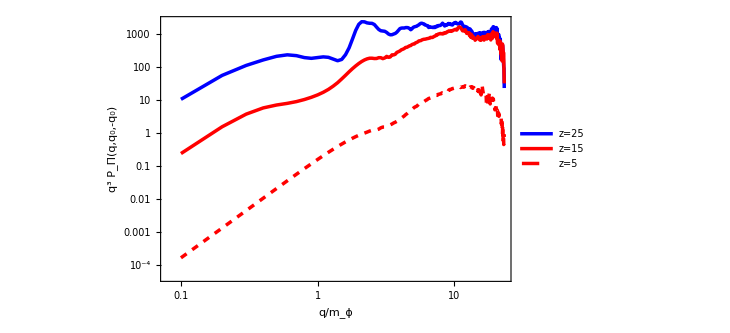

```mathematica
plotGWonshellPreheating = ListLogLogPlot[{onshellSource1,onshellSource2,onshellSource3},Joined->True,InterpolationOrder->3,Frame->True,AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[DisplayForm[FormBox[RowBox[{"q","/",Subscript["m","ϕ"]}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SuperscriptBox["q","3"],SubscriptBox["P","Π"],"(","q",",",Subscript["q","0"],",",Subscript["-q","0"],")"}],TraditionalForm]],FontSize->13]},PlotStyle->{{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5],Dashed}},
PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{"z","=","25"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{"z","=","15"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{"z","=","5"}],TraditionalForm]],FontSize->13]},LegendFunction->"Frame"],{0.8,0.25}],ImageSize->540]//Quiet
```